(e_1&&e_2&&e_3)||(e_1&&e_2&&e_4)||(e_1&&e_3&&e_4)||(e_2&&e_3&&e_4)

Piecewise[{{1, t<0}, {ⅇ^(-2587 t/500000000) (1-(1-ⅇ^(-137 t/40000000))^2) (1-(1-ⅇ^(-t/500000))^2) (1-(1-ⅇ^(-181 t/500000000))^2)^2 (ⅇ^(-873 t/500000000)+ⅇ^(-291 t/500000000) (-ⅇ^(-873 t/500000000)+ⅇ^(-291 t/250000000)+ⅇ^(-291 t/500000000) (-ⅇ^(-291 t/250000000)+ⅇ^(-291 t/500000000)+ⅇ^(-291 t/500000000) (1-ⅇ^(-291 t/500000000))))), True}}]

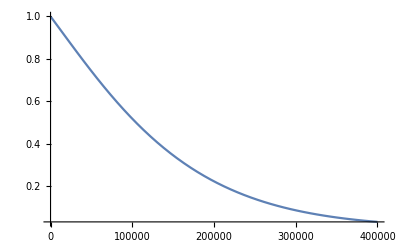

132564.

{0.99997,0.999819,0.999457}

15.1329

```mathematica
removeAll:=Remove[Evaluate[$Context<>"*"]];

removeAll

(* Считаем для сервера RH1288 *)
Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"HDD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[3425×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1];
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (*CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (*RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh1288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh1288,t]
Plot[SurvivalFunction[ℛrh1288,t]//Evaluate,{t,0,400000},PlotRange->All]
mttf=NExpectation[t,t\[Distributed]ℛrh1288]
avail = mttf/(mttf+{4,24,72})
Mean[ℛrh1288]/(24*365)//N
```

```mathematica
Subscript[d, 2]=1
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10] (*RAM *)
Array[Subscript[g, #]&,2]
```

1

d_1&&1&&d_3&&d_4&&d_5&&d_6&&d_7&&d_8&&d_9&&d_10

{g_1,g_2}

```mathematica
ℛ
```

ReliabilityDistribution[x1&&x2&&x3&&x4&&x5&&x6&&x7&&x8&&x9&&x10&&x11&&x12&&x13&&x14&&((x15&&x16&&x17)||(x15&&x16&&x18)||(x15&&x17&&x18)||(x16&&x17&&x18))&&(x19||x20)&&(x21||x22)&&(x23||x24)&&(x25||x26),{{x1,ExponentialDistribution[807/200000000]},{x2,ExponentialDistribution[559/1000000000]},{x3,ExponentialDistribution[1/25000000]},{x4,ExponentialDistribution[1/25000000]},{x5,ExponentialDistribution[1/20000000]},{x6,ExponentialDistribution[1/20000000]},{x7,ExponentialDistribution[1/20000000]},{x8,ExponentialDistribution[1/20000000]},{x9,ExponentialDistribution[1/20000000]},{x10,ExponentialDistribution[1/20000000]},{x11,ExponentialDistribution[1/20000000]},{x12,ExponentialDistribution[1/20000000]},{x13,ExponentialDistribution[1/20000000]},{x14,ExponentialDistribution[1/20000000]},{x15,ExponentialDistribution[291/500000000]},{x16,ExponentialDistribution[291/500000000]},{x17,ExponentialDistribution[291/500000000]},{x18,ExponentialDistribution[291/500000000]},{x19,ExponentialDistribution[137/40000000]},{x20,ExponentialDistribution[137/40000000]},{x21,ExponentialDistribution[1/500000]},{x22,ExponentialDistribution[1/500000]},{x23,ExponentialDistribution[181/500000000]},{x24,ExponentialDistribution[181/500000000]},{x25,ExponentialDistribution[181/500000000]},{x26,ExponentialDistribution[181/500000000]}}]

```mathematica
BooleanConvert[bexpr, "CNF"]
ReliabilityDistribution[BooleanConvert[bexpr, "CNF"], dists]
```

(x_19||x_20||x_1)&&(x_19||x_20||x_18)&&(x_19||x_17||x_18)&&(x_20||x_1||x_2)&&(x_1||x_2||x_3)&&(x_2||x_3||x_4)&&(x_3||x_4||x_5)&&(x_4||x_5||x_6)&&(x_5||x_6||x_7)&&(x_6||x_7||x_8)&&(x_7||x_8||x_9)&&(x_8||x_9||x_10)&&(x_9||x_10||x_11)&&(x_10||x_11||x_12)&&(x_11||x_12||x_13)&&(x_12||x_13||x_14)&&(x_13||x_14||x_15)&&(x_14||x_15||x_16)&&(x_15||x_16||x_17)&&(x_16||x_17||x_18)

ReliabilityDistribution[(x19||x20||x1)&&(x19||x20||x18)&&(x19||x17||x18)&&(x20||x1||x2)&&(x1||x2||x3)&&(x2||x3||x4)&&(x3||x4||x5)&&(x4||x5||x6)&&(x5||x6||x7)&&(x6||x7||x8)&&(x7||x8||x9)&&(x8||x9||x10)&&(x9||x10||x11)&&(x10||x11||x12)&&(x11||x12||x13)&&(x12||x13||x14)&&(x13||x14||x15)&&(x14||x15||x16)&&(x15||x16||x17)&&(x16||x17||x18),{{x1,ExponentialDistribution[1]},{x2,ExponentialDistribution[1]},{x3,ExponentialDistribution[1]},{x4,ExponentialDistribution[1]},{x5,ExponentialDistribution[1]},{x6,ExponentialDistribution[1]},{x7,ExponentialDistribution[1]},{x8,ExponentialDistribution[1]},{x9,ExponentialDistribution[1]},{x10,ExponentialDistribution[1]},{x11,ExponentialDistribution[1]},{x12,ExponentialDistribution[1]},{x13,ExponentialDistribution[1]},{x14,ExponentialDistribution[1]},{x15,ExponentialDistribution[1]},{x16,ExponentialDistribution[1]},{x17,ExponentialDistribution[1]},{x18,ExponentialDistribution[1]},{x19,ExponentialDistribution[1]},{x20,ExponentialDistribution[1]}}]

```mathematica
Subscript[x, 1]
```

x_1

```mathematica
(* см. ref/ReliabilityDistribution Applications

A vacuum system in a small electron accelerator contains 20 vacuum bulbs arranged in a circle.The vacuum system fails if at least three adjacent vacuum bulbs fail: *)
n=20;k=3;
bexpr=And@@Map[Or@@#&,Partition[Array[Subscript[x, #]&,n],k,1,{-1,-1}]]
dists=Array[{Subscript[x, #],ExponentialDistribution[1]}&,n]
ℛ=ReliabilityDistribution[bexpr,dists]
```

(x_19||x_20||x_1)&&(x_20||x_1||x_2)&&(x_1||x_2||x_3)&&(x_2||x_3||x_4)&&(x_3||x_4||x_5)&&(x_4||x_5||x_6)&&(x_5||x_6||x_7)&&(x_6||x_7||x_8)&&(x_7||x_8||x_9)&&(x_8||x_9||x_10)&&(x_9||x_10||x_11)&&(x_10||x_11||x_12)&&(x_11||x_12||x_13)&&(x_12||x_13||x_14)&&(x_13||x_14||x_15)&&(x_14||x_15||x_16)&&(x_15||x_16||x_17)&&(x_16||x_17||x_18)&&(x_17||x_18||x_19)&&(x_18||x_19||x_20)

{{x_1,ExponentialDistribution[1]},{x_2,ExponentialDistribution[1]},{x_3,ExponentialDistribution[1]},{x_4,ExponentialDistribution[1]},{x_5,ExponentialDistribution[1]},{x_6,ExponentialDistribution[1]},{x_7,ExponentialDistribution[1]},{x_8,ExponentialDistribution[1]},{x_9,ExponentialDistribution[1]},{x_10,ExponentialDistribution[1]},{x_11,ExponentialDistribution[1]},{x_12,ExponentialDistribution[1]},{x_13,ExponentialDistribution[1]},{x_14,ExponentialDistribution[1]},{x_15,ExponentialDistribution[1]},{x_16,ExponentialDistribution[1]},{x_17,ExponentialDistribution[1]},{x_18,ExponentialDistribution[1]},{x_19,ExponentialDistribution[1]},{x_20,ExponentialDistribution[1]}}

ReliabilityDistribution[(x19||x20||x1)&&(x20||x1||x2)&&(x1||x2||x3)&&(x2||x3||x4)&&(x3||x4||x5)&&(x4||x5||x6)&&(x5||x6||x7)&&(x6||x7||x8)&&(x7||x8||x9)&&(x8||x9||x10)&&(x9||x10||x11)&&(x10||x11||x12)&&(x11||x12||x13)&&(x12||x13||x14)&&(x13||x14||x15)&&(x14||x15||x16)&&(x15||x16||x17)&&(x16||x17||x18)&&(x17||x18||x19)&&(x18||x19||x20),{{x1,ExponentialDistribution[1]},{x2,ExponentialDistribution[1]},{x3,ExponentialDistribution[1]},{x4,ExponentialDistribution[1]},{x5,ExponentialDistribution[1]},{x6,ExponentialDistribution[1]},{x7,ExponentialDistribution[1]},{x8,ExponentialDistribution[1]},{x9,ExponentialDistribution[1]},{x10,ExponentialDistribution[1]},{x11,ExponentialDistribution[1]},{x12,ExponentialDistribution[1]},{x13,ExponentialDistribution[1]},{x14,ExponentialDistribution[1]},{x15,ExponentialDistribution[1]},{x16,ExponentialDistribution[1]},{x17,ExponentialDistribution[1]},{x18,ExponentialDistribution[1]},{x19,ExponentialDistribution[1]},{x20,ExponentialDistribution[1]}}]

```mathematica
ExponentialDistribution[λ];
With[{n=5,m=2},Binomial[n+m-1,m]];
(* Резервирование с дробной кратностью *)
pSystem[n_,m_,t_]:=∑_(i=0)^m (Binomial[n,i](1-PDF[ExponentialDistribution[λ], t])^i PDF[ExponentialDistribution[λ],t]^(n-i))
```

```mathematica
ExponentialDistribution[λ]
```

ExponentialDistribution[λ]

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
pSystem[2,4,t] /. {λ->0.05} //N
pSystem[2,4,1] /. {λ->0.05} //N
```

(1.-1. (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}]))^2+2. (1.-1. (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])) (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])+(Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])^2

1.

1/λ_1+1/λ_2-1/(λ_1+λ_2)

Piecewise[{{1, t<0}, {ⅇ^(-t (λ_1+λ_2)) (-1+ⅇ^(t λ_1)+ⅇ^(t λ_2)), True}}]

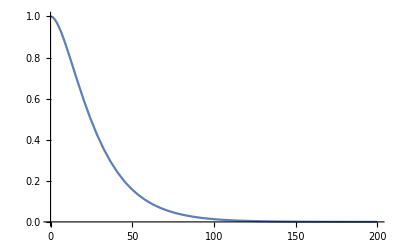

```mathematica
ℛ=ReliabilityDistribution[x||y||(x&&y),{{x,ExponentialDistribution[Subscript[λ, 1]]},{y,ExponentialDistribution[Subscript[λ, 2]]}}];
Mean[ℛ]
SurvivalFunction[ℛ,t]//Simplify
Plot[SurvivalFunction[ℛ,t] /. {Subscript[λ, 1]->0.05,Subscript[λ, 2]->0.05},{t,0,200},PlotRange->All]
```

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

```mathematica
BooleanCountingFunction[2,4][a,b,c, d]
BooleanConvert[%]
```

BooleanCountingFunction[2,4][a,b,c,d]

(!a&&!b)||(!a&&!c)||(!a&&!d)||(!b&&!c)||(!b&&!d)||(!c&&!d)

```mathematica
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[Subscript[λ, i]],{i,3}];
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[λ],{i,3}];
bcf=BooleanCountingFunction[{3,4},4][a,b,c,d]
UnateQ[bcf]
BooleanConvert[bcf]
(*ℛ=ReliabilityDistribution[x ||y,{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}]*)
ℛ=ReliabilityDistribution[BooleanCountingFunction[{2,3},3][x,y,z],{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}]

λ=0.05
SurvivalFunction[ℛ,t]//Simplify
Mean[ℛ]
N[%]
Probability[t<0.5,t\[Distributed]ℛ]
```

```mathematica
Mean[ℛ] // N
```

BooleanCountingFunction::bspec: BooleanCountingFunction[{2.,3.},3.] is not a valid BooleanCountingFunction specification.

ReliabilityDistribution::vundef: The variable BooleanCountingFunction[{2.,3.},3.][x1,x2,x3] has no associated distribution.

Mean[ReliabilityDistribution[BooleanCountingFunction[{2.,3.},3.][x1,x2,x3],{{x1,ExponentialDistribution[0.05]},{x2,ExponentialDistribution[0.05]},{x3,ExponentialDistribution[0.05]}}]]

```mathematica
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[Subscript[λ, i]],{i,3}]
Subscript[𝒟, 1]
ℛ=ReliabilityDistribution[BooleanConsecutiveFunction[2,3][x,y,z],{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}];
SurvivalFunction[ℛ,t]//Simplify
```

{ExponentialDistribution[λ_1],ExponentialDistribution[λ_2],ExponentialDistribution[λ_3]}

ExponentialDistribution[λ_1]

Piecewise[{{1, t<0}, {ⅇ^(-t (λ_1+λ_2+λ_3)) (-1+ⅇ^(t λ_1)+ⅇ^(t λ_3)), True}}]